Smoothing a list and filtering a time series

#### List showing periodic functions plus noise

Construct a list of points from two periodic functions plus noise:
The frequency of the sin wave at each point is offset by a small random number to which a random noise and a cosine wave are added. 
Table[ expression , {n, NDP} ] evaluates the expression for n= 1,2,3 ...NPD

```mathematica
NDP=10000;
dt=0.1;
freq1=0.011;
freq2=0.005;
rand1 = 0.0002;
rand2 = 0.5;
NDP*dt;
datalist = Table[N[
Sin[(freq1+RandomReal[{-rand1,rand1}])*2 Pi*dt* n]
+ 0.5*RandomReal[{-rand2,rand2}]  
+ 0.2*Cos[freq2*2 Pi*dt* n]  
],
{n,NDP}]
```

Plot the list. Note the x-axis is the data point number, not time.

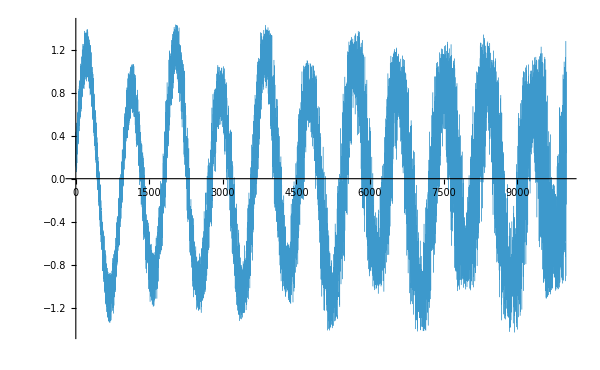

```mathematica
ListLinePlot[datalist,ImageSize->{600,400},PlotStyle->Thickness[0.0005]]
```

Zoom in to the region [6,000, 8,000]:

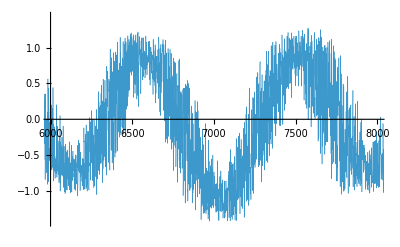

```mathematica
ListLinePlot[datalist,PlotRange->{{6000,8000},All},PlotStyle->Thickness[0.001]]
```

#### Smoothing the list

Plot a moving average in the same region, smoothing using a box size of 2:

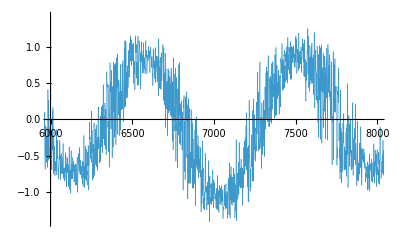

```mathematica
ListLinePlot[MovingAverage[datalist,2],PlotRange->{{6000,8000},All},PlotStyle->Thickness[0.001]]
```

Re-plot the moving average, but now with a smoothing box of length 10:

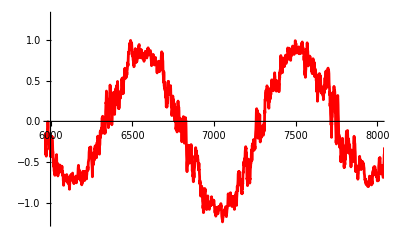

```mathematica
ListLinePlot[MovingAverage[datalist,#]& /@ {10},PlotRange->{{6000,8000},All},PlotStyle->Red ]
```

Display the length of the list and the smoothed list:

```mathematica
Dimensions[datalist]
Dimensions[MovingAverage[datalist,10]]
```

{10000}

{9991}

Show a combined plot with
(1) the original list (black)
(2) smoothed with box size 10 (red)
(3) smoothed with box size 100 (blue)
(4) smoothed with box size 500 (light red)

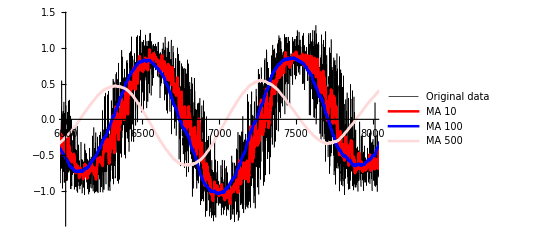

```mathematica
Show[ListLinePlot[datalist,PlotRange->{{6000,8000},All},PlotStyle->{Black,Thickness[0.001]},PlotLegends->{"Original data"}],
ListLinePlot[MovingAverage[datalist,#]& /@ {10,100,500},PlotRange->{{6000,8000},All},
PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]},{LightRed,Thickness[0.005]}},
PlotLegends->{"MA 10","MA 100","MA 500"}]]
```

Why is this shifted to the left the more it is smoothed? (think about the period of the waves)

Now show the same but for the first 2000 points, with smoothing boxes of size 10, 100, and 200.

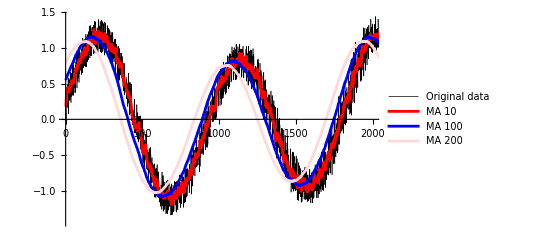

```mathematica
Show[ListLinePlot[datalist,PlotRange->{{0,2000},All},PlotStyle->{Black,Thickness[0.001]},PlotLegends->{"Original data"}],
ListLinePlot[MovingAverage[datalist,#]& /@ {10,100,200},PlotRange->{{0,2000},All},PlotStyle->{Red,Blue,LightRed},PlotLegends->{"MA 10","MA 100","MA 200"}]]
```

This plot shows a moving median as well as a moving average, with a smoothing box size of 20.

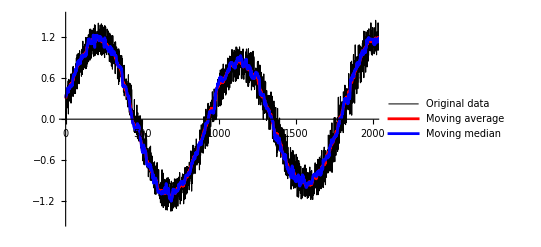

```mathematica
ListLinePlot[{datalist,MovingAverage[datalist,20],MovingMedian[datalist,20]},
PlotRange->{{0,2000},{-1.5,1.5}},PlotStyle->{{Black,Thickness[0.002]},Red,Blue},
PlotLegends->{"Original data","Moving average","Moving median"}]
```

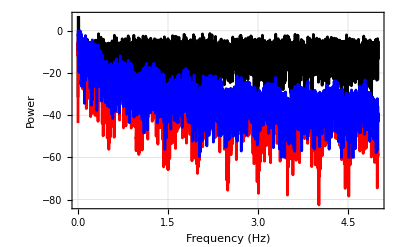

```mathematica
Show[{Periodogram[datalist[[20;;]],PlotStyle->{Black,Thickness[0.002]},SampleRate->10],Periodogram[MovingAverage[datalist,20],PlotStyle->Red,SampleRate->10],Periodogram[MovingMedian[datalist,20],PlotStyle->Blue,SampleRate->10] },PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Power"},GridLines->Automatic]
```

#### Time series

Now let’s make a time series out of it with paired data and time as independent variable. The sampling time is dt = 0.1.
Length of a table with points separated by dt:

```mathematica
Length[Table[n*dt,{n,NDP}]]
```

10000

Convert to a list of times:

```mathematica
timelist=Table[n*dt,{n,NDP}];
Dimensions[timelist]
```

{10000}

Match each time point to a point in the list to form a time series:

```mathematica
timedata = {timelist[[#]],datalist[[#]]}& /@ Range[NDP]
```

The time series data is 2-D:

```mathematica
Dimensions[timedata]
```

{10000,2}

Plot the time series:

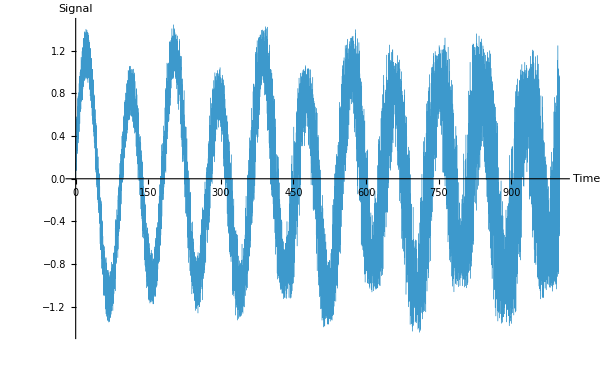

```mathematica
ListLinePlot[timedata,AxesLabel->{"Time","Signal"},ImageSize->{600,400},PlotStyle->Thickness[0.0005]]
```

Note the x-axis is now scaled correctly.

Create a TimeSeries object from the time series

```mathematica
ts=TimeSeries[timedata]
```

TimeSeries[…]

#### Filtering the time series in the time domain

Now we filter the time series using MeanFilter. 
This is the same principle as the MovingAverage used above, but the data is now averaged forwards and backwards in time.
The window length T in MeanFilter is specified in terms of real time, not number of data points. 
If you specify a window length of T, the data at t will be replaced with the mean from t-T to t+T.
If you put T = 0 you will get the original time series back.

Filter with T = 1s.

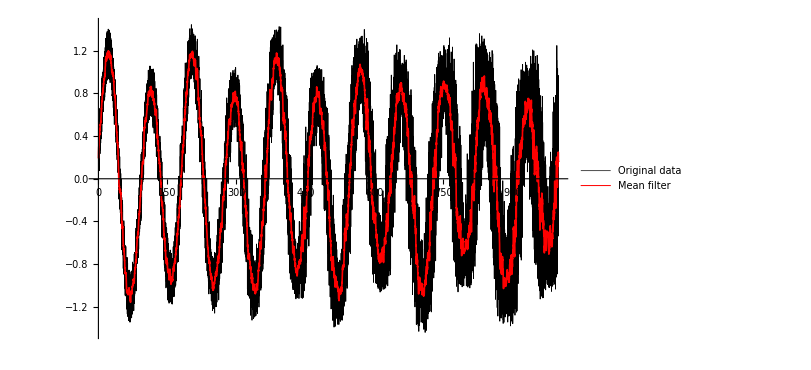

```mathematica
ListLinePlot[{ts,MeanFilter[ts,1]},ImageSize->{600,400},
PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.002]}},
PlotLegends->{"Original data","Mean filter"}]
```

Filter with T = 0.5s, showing just the first 100s.

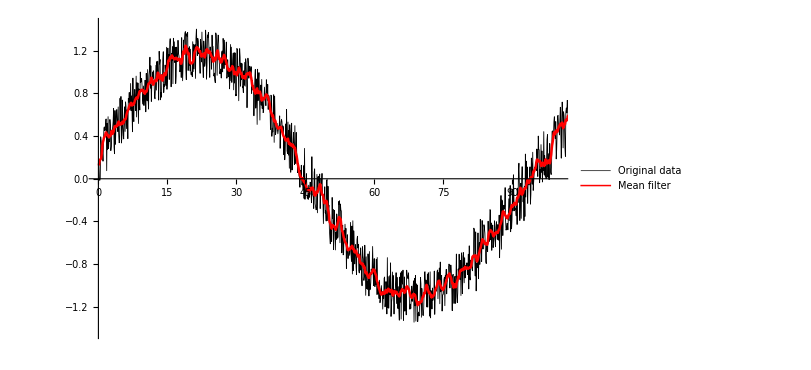

```mathematica
ListLinePlot[{ts,MeanFilter[ts,0.5]},PlotRange->{{0,100},All},
PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.003]}},
ImageSize->{600,400},PlotLegends->{"Original data","Mean filter"}]
```

Filter with T = 0.1s and T = 0.3s, along with the original time series.

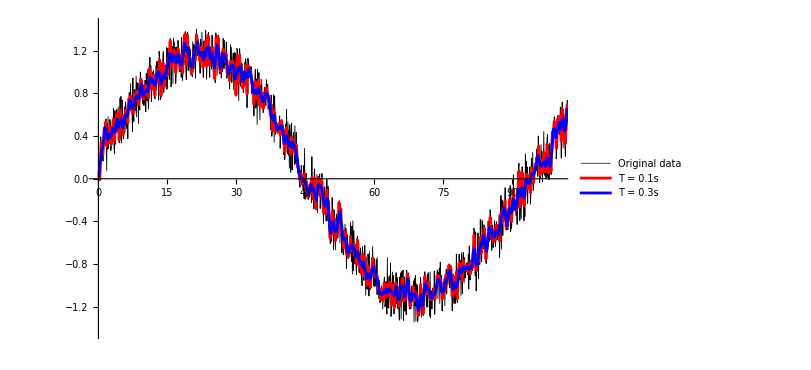

```mathematica
ListLinePlot[MeanFilter[ts,#]& /@{0,0.1,0.3},PlotRange->{{0,100},All},
PlotStyle->{{Black,Thickness[0.001]},Red,Blue},ImageSize->{600,400},PlotLegends->{"Original data","T = 0.1s", "T = 0.3s"}]
```

Let’s plot some more filtered versions of the time series.
Filtered using a mean filter with T = 0, 0.1, 0.3, 1, and 5s, at the end of the time series.

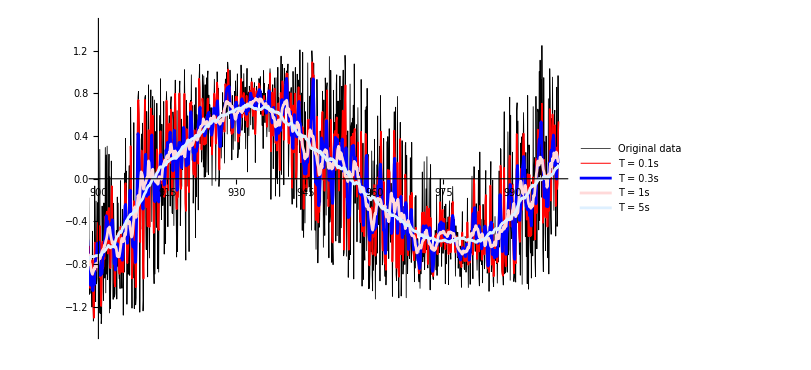

```mathematica
ListLinePlot[MeanFilter[ts,#]& /@{0,0.1,0.3,1,5},PlotRange->{{900,1000},All},
PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.002]},Blue,LightRed,LightBlue},ImageSize->{600,400},
PlotLegends->{"Original data","T = 0.1s","T = 0.3s","T = 1s","T = 5s"}]
```

Thread::tdlen: Objects of unequal length in {{{6,7},{7,6},{6,7},{7,5},{5,4},{4,8},{8,3},{3,1},{1,2}},{4.44089×10^-16,0.1,0.1,0.1,0.1,0.1,0.1}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{14,15},{15,14},{14,15},{15,11},{11,8},{8,16},{16,7},{7,2},{2,3},{3,21},{21,12},{12,22},{22,1},{1,5},{5,20},{20,10},{10,6},{6,4},{4,13},{13,17},{17,9},{9,19},{19,18}},{4.44089×10^-16,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{9,10},{10,9},{9,10},{10,18},{18,6},{6,14},{14,8},{8,1},{1,21},{21,5},{5,3},{3,15},{15,16},{16,11},{11,7},{7,22},{22,4},{4,20},{20,13},{13,19},{19,2},{2,17},{17,12}},{8.88178×10^-16,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

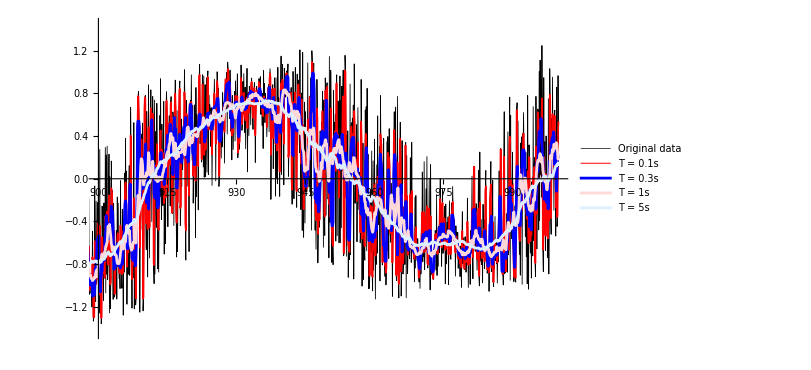

```mathematica
ListLinePlot[MedianFilter[ts,#]& /@{0,0.1,0.3,1,5},PlotRange->{{900,1000},All},
PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.002]},Blue,LightRed,LightBlue},ImageSize->{600,400},
PlotLegends->{"Original data","T = 0.1s","T = 0.3s","T = 1s","T = 5s"}]
```

Plot the end of the time series with both mean and median filters with T = 0.3s.
The second one zooms in to the region 900-930s.

Thread::tdlen: Objects of unequal length in {{{6,7},{7,6},{6,7},{7,5},{5,4},{4,8},{8,3},{3,1},{1,2}},{4.44089×10^-16,0.1,0.1,0.1,0.1,0.1,0.1}} cannot be combined.

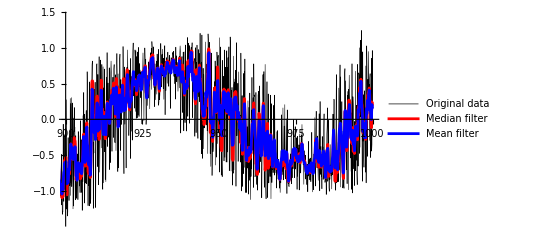

Thread::tdlen: Objects of unequal length in {{{6,7},{7,6},{6,7},{7,5},{5,4},{4,8},{8,3},{3,1},{1,2}},{4.44089×10^-16,0.1,0.1,0.1,0.1,0.1,0.1}} cannot be combined.

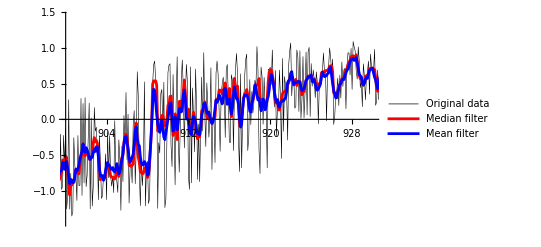

```mathematica
ListLinePlot[{ts,MedianFilter[ts,0.3],MeanFilter[ts,0.3]},PlotRange->{{900,1000},All},
PlotStyle->{{Black,Thickness[0.001]},Red,Blue},PlotLegends->{"Original data","Median filter","Mean filter"}]
ListLinePlot[{ts,MedianFilter[ts,0.3],MeanFilter[ts,0.3]},PlotRange->{{900,930},All},
PlotStyle->{{Black,Thickness[0.001]},Red,Blue},PlotLegends->{"Original data","Median filter","Mean filter"}]
```

Notice that the shift to the left has disappeared now we are working with a time series. 
This is because the average is centred on each data point. 

Finally, here is the example from earlier that was progressively shifted to the left as the box window size increased.
A window width of 500 with MovingAverage is equivalent to a window width of 500*dt/2 = 25 with MeanFilter.
The smoothed curves are approximately the same but no longer shifted to the left.

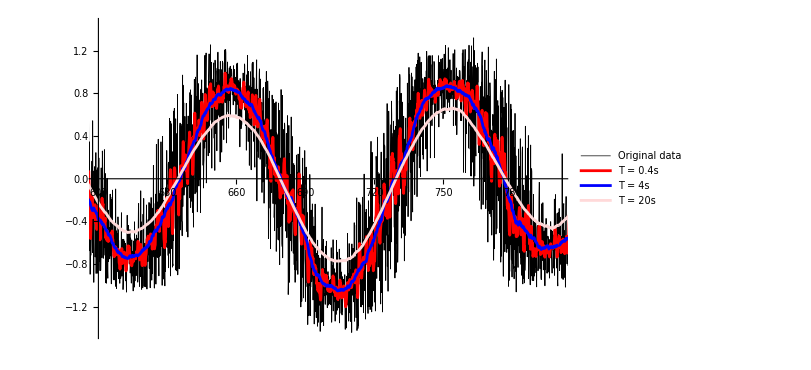

```mathematica
ListLinePlot[MeanFilter[ts,#]& /@{0,0.4,4, 20},PlotRange->{{600,800},All},
PlotStyle->{{Black,Thickness[0.001]},Red,Blue,LightRed},ImageSize->{600,400},
PlotLegends->{"Original data","T = 0.4s","T = 4s", "T = 20s"}]
```

```mathematica
ListLinePlot[(MeanFilter[ts,#1]&)/@{0,0.4,4,20},PlotTheme->Automatic,PlotRange->{{600,800},All},PlotStyle->{{GrayLevel[0],Thickness[0.001]},RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[1,0.85,0.85]},ImageSize->{600,400},PlotLegends->{"Original data","T = 0.4s","T = 4s","T = 20s"}]
```

-Graphics-

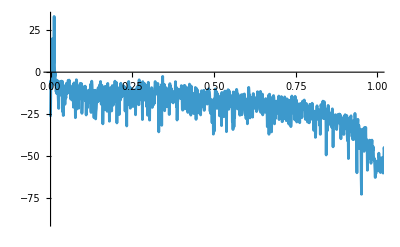

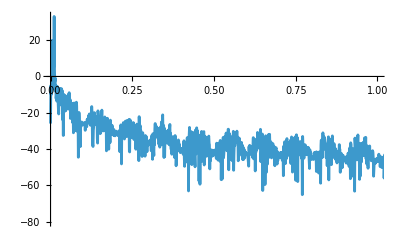

```mathematica
Periodogram[MeanFilter[ts,0.5]["Values"], SampleRate->10, PlotRange->{{0,1},All}]
Periodogram[MeanFilter[ts,5]["Values"], SampleRate->10, PlotRange->{{0,1},All}]
```

Notice how the power at higher frequencies die down considerably as the window size is increased

#### Gaussian filter

Now let’s try a Gaussian filter instead of a mean filter. 
This filters the data using a Gaussian (normal) function with σ = T / 2 rather than a rectangular function of width 2T.
The main difference between these two filters comes in the frequency domain rather than the time domain .

Filter using T = 10s:

```mathematica
gaussfilt=GaussianFilter[ts,10]
```

TimeSeries[…]

Plot the original and filtered time series:

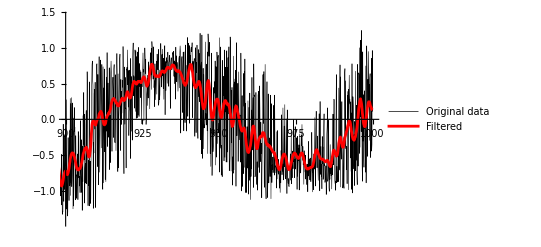

```mathematica
ListLinePlot[{ts,gaussfilt},PlotRange->{{900,1000},All},
PlotStyle->{{Black,Thickness[0.001]},Red},
PlotLegends->{"Original data","Filtered"}]
```

Plot with T = 0.1s, 1s, 10s, and 50s:

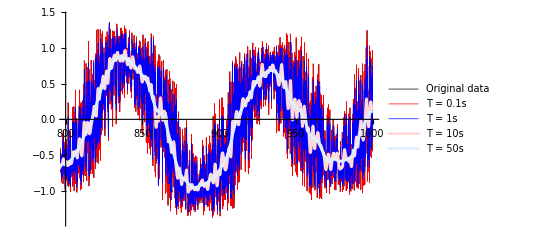

```mathematica
ListLinePlot[GaussianFilter[ts,#]& /@{0,0.1,1,10,50},PlotRange->{{800,1000},All},
PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.001]},{Blue,Thickness[0.001]},LightRed,LightBlue},
PlotLegends->{"Original data","T = 0.1s","T = 1s", "T = 10s", "T = 50s"}]
```

Compare the Gaussian filter using T = 10 s (2 . standard deviation) with the original mean filter. 
The equivalent T for the mean filter is 5 s (window width = 10s)

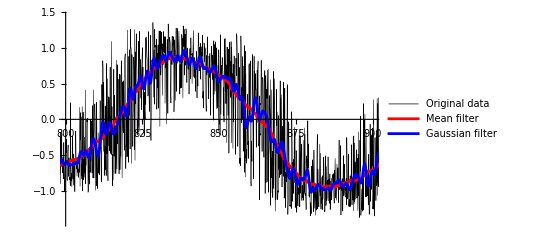

```mathematica
ListLinePlot[{ts,MeanFilter[ts,5],GaussianFilter[ts,10]},
PlotRange->{{800,900},All},PlotStyle->{{Black,Thickness[0.001]},Red,Blue},
PlotLegends->{"Original data","Mean filter","Gaussian filter"}]
```

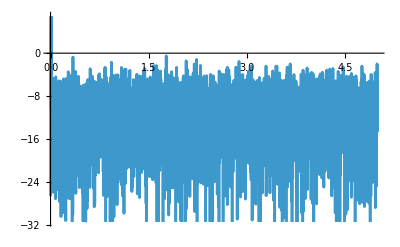

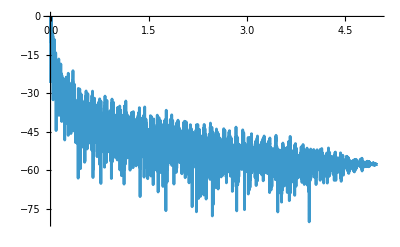

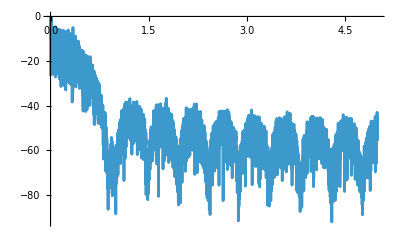

```mathematica
Periodogram[ts["Values"], SampleRate->10]
Periodogram[MeanFilter[ts,5]["Values"], SampleRate->10]
Periodogram[GaussianFilter[ts,10]["Values"], SampleRate->10]
```

#### Other filters in the time domain

Now plot using a minimum filter (replaces each value with the minimum value within the neighbourhood), using various window lengths:

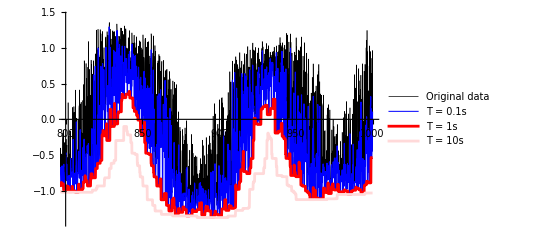

```mathematica
ListLinePlot[MinFilter[ts,#]& /@{0,0.1,1,10},PlotRange->{{800,1000},All},
PlotStyle->{{Black,Thickness[0.001]},{Blue,Thickness[0.002]},Red,LightRed},
PlotLegends->{"Original data","T = 0.1s","T = 1s", "T = 10s"}]
```

And with a maximum filter (equivalent):

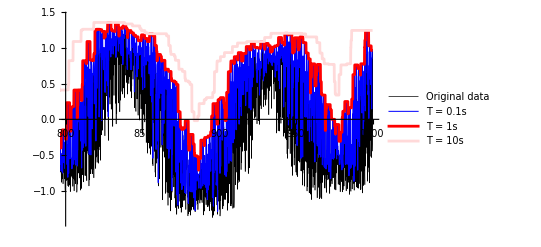

```mathematica
ListLinePlot[MaxFilter[ts,#]& /@{0,0.1,1,10},PlotRange->{{800,1000},All},
PlotStyle->{{Black,Thickness[0.001]},{Blue,Thickness[0.002]},Red,LightRed},
PlotLegends->{"Original data","T = 0.1s","T = 1s", "T = 10s"}]
```

Finally, plot both the minimum and maximum alongside the original:

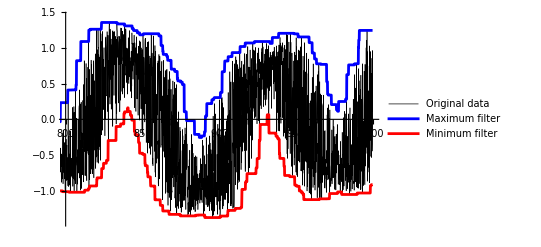

```mathematica
ListLinePlot[{ts,MaxFilter[ts,5],MinFilter[ts,5]},PlotRange->{{800,1000},All},
PlotStyle->{{Black,Thickness[0.001]},Blue,Red},
PlotLegends->{"Original data","Maximum filter","Minimum filter"}]
```

### Frequency domain filtering

Low-pass filter
Now apply a Low-pass filter. This converts the time series to the frequency domain, removes almost all power from the spectrum above a particular frequency, 
and then converts back to the time domain. It lets low frequencies pass through.

Apply to the original time series, cutting off just above frequency .5 Hz to keep both the periods
The choice of the third parameter “kernel” is based on the discussion at 
https://mathematica.stackexchange.com/questions/153414/high-pass-filter-without-losing-detail

```mathematica
kernel=Round[Length[ts["Values"]]/10];
lpfiltered=LowpassFilter[ts["Values"],2*Pi*.5,kernel, SampleRate->10]
```

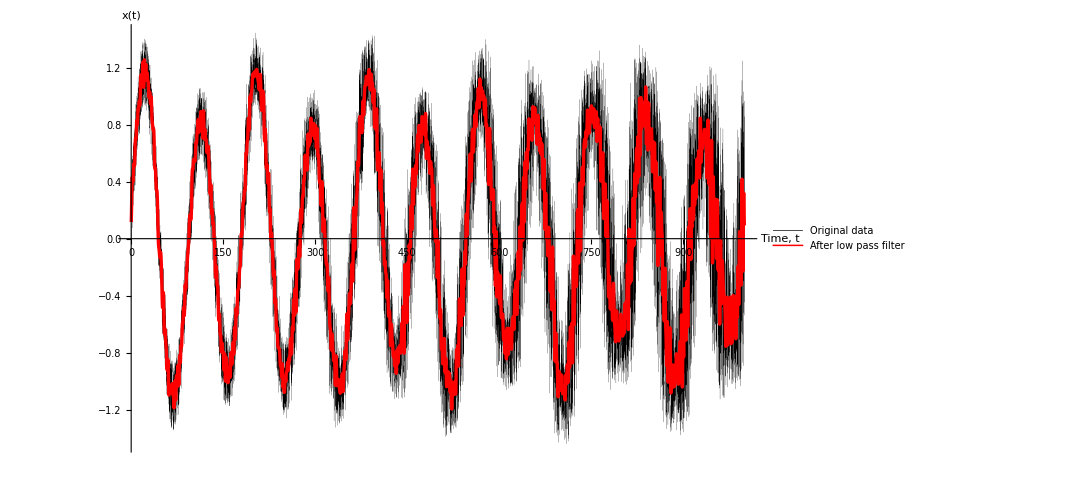

```mathematica
newtimepslp = {timelist[[#]],lpfiltered[[#]]}& /@ Range[Length[lpfiltered]];
ListLinePlot[{timedata,newtimepslp},PlotLegends->{"Original data","After low pass filter"},
AxesLabel->{"Time, t","x(t)"},ImageSize->{800,400},
PlotRange->Automatic,PlotStyle->{{Black,Thickness[0.0001]},{Red,Thickness[0.003]}}]
```

Notice how only the low frequencies are passed, and the high frequency noise is cut off. Lets look at the FT.

-Graphics-

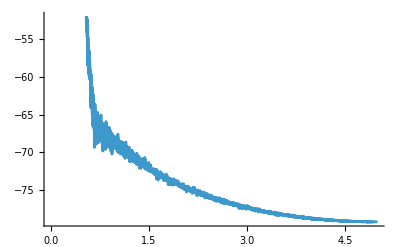

```mathematica
Periodogram[ts["Values"], SampleRate->10]
Periodogram[lpfiltered, SampleRate->10]
```

The higher frequencies are reduced heavily

#### High pass

Now we try a high pass filter. If we keep a cut off above the frequencies of the periods, only the noise should survive

```mathematica
kernel=Round[Length[ts["Values"]]/10];
hpfiltered=HighpassFilter[ts["Values"],2*Pi*.5,kernel, SampleRate->10]
```

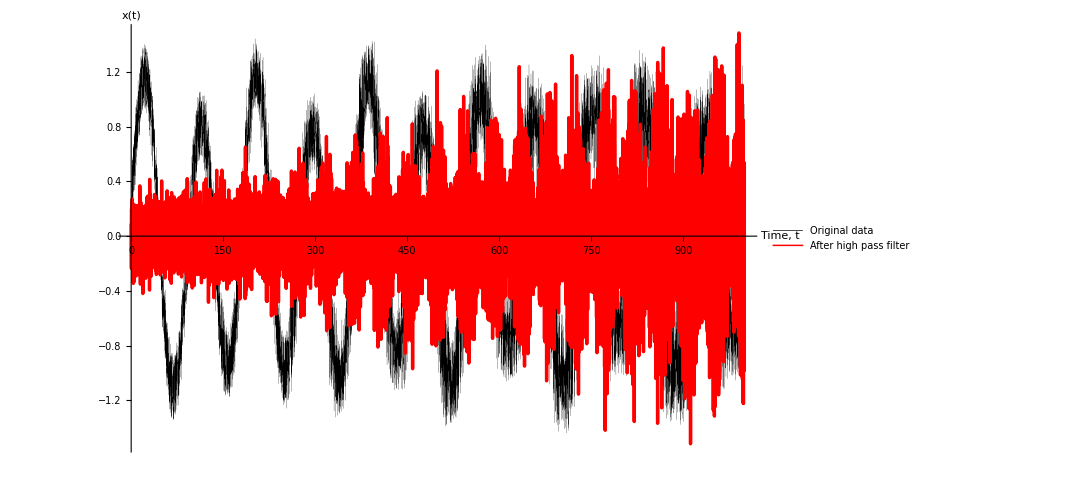

```mathematica
newtimepshp = {timelist[[#]],hpfiltered[[#]]}& /@ Range[Length[lpfiltered]];
ListLinePlot[{timedata,newtimepshp},PlotLegends->{"Original data","After high pass filter"},
AxesLabel->{"Time, t","x(t)"},ImageSize->{800,400},
PlotRange->Automatic,PlotStyle->{{Black,Thickness[0.0001]},{Red,Thickness[0.003]}}]
```

As expected, only the noise survives, and helps us identify the change in the noise levels over time.

-Graphics-

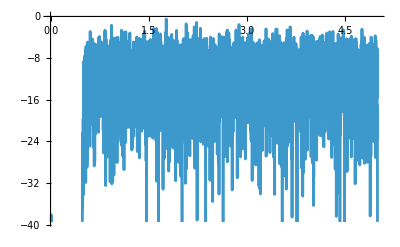

```mathematica
Periodogram[ts["Values"], SampleRate->10]
Periodogram[hpfiltered, SampleRate->10]
```

#### Bandpass filter

This is a bit more painful with our choice of periods in the beginning, but lets try. (remember, our frequencies were .005 and .011)

```mathematica
bpfiltered1=BandpassFilter[ts["Values"],{2*Pi*.001,2*Pi*.1},kernel, SampleRate->10];
```

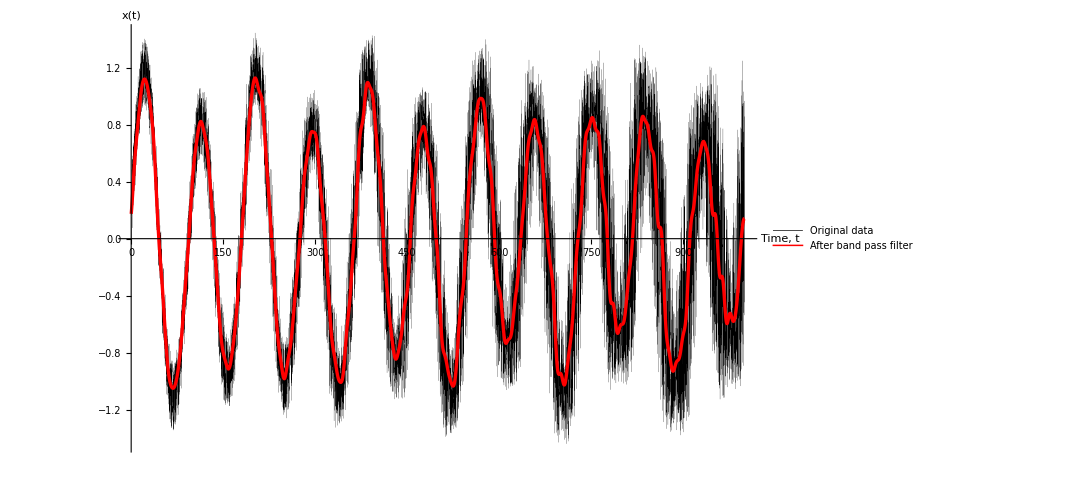

```mathematica
newtimepsbp = {timelist[[#]],bpfiltered1[[#]]}& /@ Range[Length[lpfiltered]];
ListLinePlot[{timedata,newtimepsbp},PlotLegends->{"Original data","After band pass filter"},
AxesLabel->{"Time, t","x(t)"},ImageSize->{800,400},
PlotRange->Automatic,PlotStyle->{{Black,Thickness[0.0001]},{Red,Thickness[0.003]}}]
```

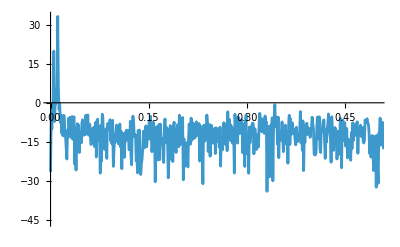

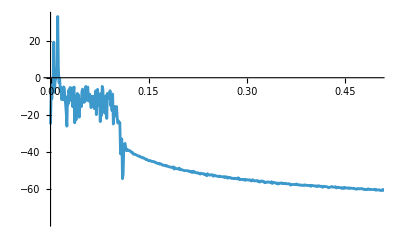

```mathematica
Periodogram[ts["Values"], SampleRate->10, PlotRange->{{0,.5},All}]
Periodogram[bpfiltered1, SampleRate->10, PlotRange->{{0,.5},All}]
```

Last, lets try a bandstop filter

```mathematica
bsfiltered=BandstopFilter[ts["Values"],{2*Pi*.0001,2*Pi*.01},kernel, SampleRate->10];
```

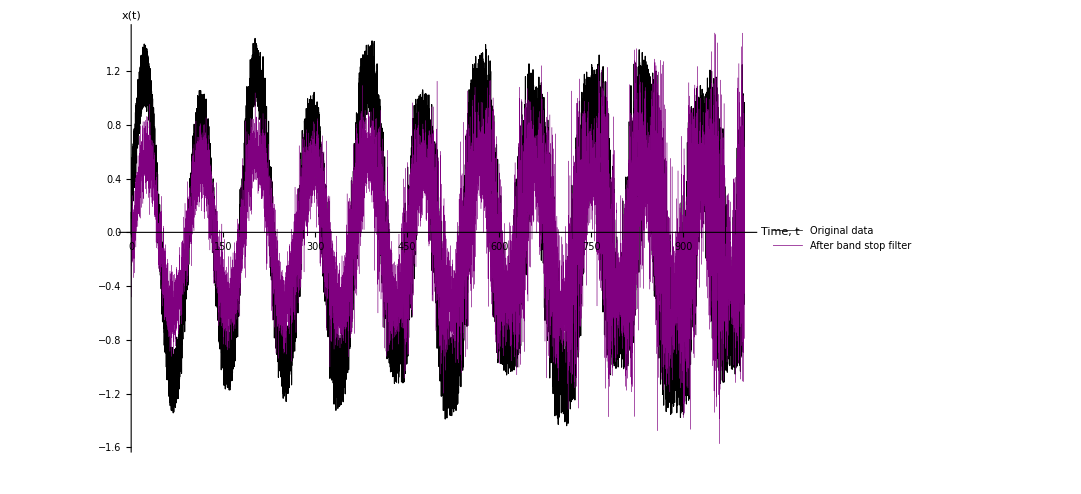

```mathematica
newtimepsbs = {timelist[[#]],bsfiltered[[#]]}& /@ Range[Length[bsfiltered]];
ListLinePlot[{timedata,newtimepsbs},PlotLegends->{"Original data","After band stop filter"},
AxesLabel->{"Time, t","x(t)"},ImageSize->{800,400},
PlotRange->Automatic,PlotStyle->{{Black,Thickness[0.001]},{Purple,Thickness[0.0003]}}]
```

-Graphics-

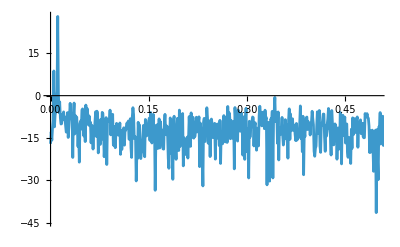

```mathematica
Periodogram[ts["Values"], SampleRate->10, PlotRange->{{0,.5},All}]
Periodogram[bsfiltered, SampleRate->10, PlotRange->{{0,.5},All}]
```

This reduces the peak at .005 considerably